```mathematica
notebookDir = NotebookDirectory[];

importdataFolders = FileNames["Board*",notebookDir];
importdata = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",importdataFolders[[board]]]),{board,1,Dimensions[importdataFolders][[1]]}];

datapathOld = notebookDir<>"Single_Board_2_221021\\";
importdataOld = Import[#,"Table"]&/@(FileNames[datapathOld<>"\\*.txt"]);

datapathNew=notebookDir<>"New Board 2\\";
importdataNew = Import[#,"Table"]&/@(FileNames[datapathNew<>"\\*.txt"]);
```

```mathematica
(*datapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\Zurich Instruments\\";
importdataFolders = FileNames["2021*",datapath];
importdata = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",importdataFolders[[board]]]),{board,1,Dimensions[importdataFolders][[1]]}];*)
```

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];

boards = {1,2,3,4,5};

RShunt = 10;
```

```mathematica
frequencies = Table[(ToExpression[StringDelete[importdata[[1,2*j-1,6+i,1]],","]]),{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

voltage1 = Table[(ToExpression[StringDelete[importdata[[board,2*j-1,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdata[[board,2*j-1,6+i,3]]])/360],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

voltage2 = Table[(ToExpression[StringDelete[importdata[[board,2*j,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdata[[board,2*j,6+i,3]]])/360],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

absImpedance = Table[{frequencies[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]],Abs[(voltage1[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]])*RShunt/((voltage2[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]]))]},{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

argImpedance = Table[{frequencies[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]],-Arg[(voltage1[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]])*RShunt/(-(voltage2[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]]))]},{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},{i,1,Length[importdata[[1,1,7;;,-1]]]}];
```

```mathematica
voltageDataOld= Table[importdataOld[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importdataOld][[1]]},{entry,1,4}];

voltage1JOld = Table[Transpose[{voltageDataOld[[j,1,;;,1]]*1000,voltageDataOld[[j,1,;;,2]],voltageDataOld[[j,3,;;,2]]}],{j,1,Dimensions[importdataOld][[1]]}];

voltage2JOld = Table[Transpose[{voltageDataOld[[j,1,;;,1]]*1000,voltageDataOld[[j,2,;;,2]],voltageDataOld[[j,4,;;,2]]}],{j,1,Dimensions[importdataOld][[1]]}];

frequencyArray = voltage1JOld[[1,;;,1]];

impedancesJOrderedOld = Table[{frequencyArray[[freq]],(RShunt*(voltage2JOld[[j,freq,2]])*Exp[I(voltage2JOld[[j,freq,3]])*2π/360])/(((voltage1JOld[[j,freq,2]])*Exp[I(voltage1JOld[[j,freq,3]])*2π/360])-((voltage2JOld[[j,freq,2]])*Exp[I(voltage2JOld[[j,freq,3]])*2π/360]))},{j,1,Dimensions[importdataOld][[1]]},{freq,1,Length[frequencyArray]}];

ImpedancesArrayOld = Table[Abs[impedancesJOrderedOld[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]]]]],{x,1,8},{y,1,8},{sub,1,2}];


voltage1JNew = Table[(ToExpression[StringDelete[importdataNew[[2*j-1,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataNew[[2*j-1,6+i,3]]])/360],{j,1,Dimensions[importdataNew][[1]]/2},{i,1,Length[importdataNew[[1,7;;,-1]]]}];

voltage2JNew = Table[(ToExpression[StringDelete[importdataNew[[2*j,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataNew[[2*j,6+i,3]]])/360],{j,1,Dimensions[importdataNew][[1]]/2},{i,1,Length[importdataNew[[1,7;;,-1]]]}];

impedancesJOrderedNew = Table[{frequencies[[1,freq]],(RShunt*(voltage1JNew[[j,freq]]))/(((voltage2JNew[[j,freq]])))},{j,1,Dimensions[voltage1JNew][[1]]},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];
```

```mathematica
interpolationVoltagesOld = Table[Interpolation[Abs[ImpedancesArrayOld[[x,y,sub]]]],{x,1,8},{y,1,8},{sub,1,2}];

interpolationVoltagesNew = Table[Interpolation[Abs[impedancesJOrderedNew[[j]]]],{j,1,Dimensions[voltage1JNew][[1]]}];

completeInterpolation = Table[Which[x==1,
Which[y==7 ,interpolationVoltagesNew[[sub]],y==8,interpolationVoltagesNew[[2+sub]],True,interpolationVoltagesOld[[x,y,sub]]],
True,interpolationVoltagesOld[[x,y,sub]]
],{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
meanOld = Table[Mean[Flatten[Table[interpolationVoltagesOld[[x,y,sub]][frequencies[[1,freq]]],{x,1,8},{y,1,8}]]],{sub,1,2},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];

meanNew2 = Table[Mean[Flatten[Table[completeInterpolation[[x,y,sub]][frequencies[[1,freq]]],{x,1,8},{y,1,8}]]],{sub,1,2},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];
```

InterpolatingFunction::dmval: Input value {5.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of StyleBox[RowBox[{\"InterpolatingFunction\", \"::\", \"dmval\"}], \"MessageName\"] will be suppressed during this calculation.

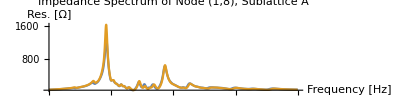

```mathematica
Plot[{interpolationVoltagesOld[[1,7,1]][ω],completeInterpolation[[1,7,1]][ω]},{ω,frequencies[[1,1]],frequencies[[1,-1]]},PlotRange->All,AspectRatio->1/4,ImageSize->Full,AxesLabel->{"Frequency [Hz]","Res. ["<>ToString[Ω]<>"]"},PlotLegends->{"Impedance Spectrum with Old Coil","Impedance Spectrum with New Coil"},PlotLabel->"Impedance Spectrum of Node (1,8), Sublattice A",Ticks->Automatic]
```

```mathematica
2.5*10^6 -frequencies[[1,170]]
```

145291.

```mathematica
subAFreqRange = 130;;250;
subBFreqRange = 50;;130;

meanAbs = Table[Mean[Flatten[absImpedance[[;;,;;,board,sub,i,2]]]],{board,1,Dimensions[importdata][[1]],1},{sub,1,2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

meanArg = Table[Mean[Flatten[argImpedance[[;;,;;,board,sub,i,2]]]],{board,1,Dimensions[importdata][[1]],1},{sub,1,2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

meanAbsForPeak = Table[Mean[Flatten[absImpedance[[;;,;;,;;,sub,i,2]]]],{sub,1,2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];
```

```mathematica
peakSubABPosVals = Table[{Position[meanAbsForPeak,Max[meanAbsForPeak[[1,If[freqs==1,170,173]]]]][[1,2]], Position[meanAbsForPeak,Max[meanAbsForPeak[[2,If[freqs==1,170,173]]]]][[1,2]]},{freqs,1,2}];
```

```mathematica
deviationOfNodesNew2 = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[completeInterpolation[[x,y,sub]][frequencies[[1,peakSubABPos[[freqs,sub]]]]]]-meanNew2[[sub,peakSubABPos[[freqs,sub]]]])/(meanNew2[[sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];

deviationOfNodesBoard2 = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[interpolationVoltagesOld[[x,y,sub]][frequencies[[1,peakSubABPos[[freqs,sub]]]]]]-meanOld[[sub,peakSubABPos[[freqs,sub]]]])/(meanOld[[sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];

completeDeviationBoard2 = Table[If[board==1,deviationOfNodesBoard2,deviationOfNodesNew2],{board,1,2}];
```

```mathematica
deviationOfNodes = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[Abs[absImpedance[[x,y,board,sub,peakSubABPos[[freqs,sub]],2]]]]-meanAbs[[board,sub,peakSubABPos[[freqs,sub]]]])/(meanAbs[[board,sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{board,1,Dimensions[importdata][[1]],1},{sub,1,2}];

completeDeviationOfNodes = Table[If[board!=2,deviationOfNodes[[;;,;;,;;,Which[board< 2,board,board>2,board-1,True,0],;;]],deviationOfNodesBoard2]
,{board,1,Dimensions[importdata][[1]]+1,1}];
```

```mathematica
cellsHistMulti =Table[{i,i},{i,8}];

freqLabels = Table[Round[frequencies[[1,peakSubABPosVals[[freqs,sub]]]]/10^6,0.01],{freqs,1,2},{sub,1,2}];

deviationHist = Table[DiscretePlot3D[Abs[completeDeviationOfNodes[[board,freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{0.3,"20"},{0.5,"40"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from mean value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" of board "<>ToString[board]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{board,1,Dimensions[completeDeviationOfNodes][[1]]},{sub,1,2}];
```

```mathematica
deviationHistOldVSNew = Table[DiscretePlot3D[Abs[completeDeviationBoard2[[board,freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{0.3,"20"},{0.5,"40"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis",Rotate["Deviation in %",π/2]},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from mean value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{board,1,Dimensions[completeDeviationBoard2][[1]]},{sub,1,2}];
```

```mathematica
Manipulate[deviationHist[[freqs,board,sub]],{freqs,1,2,1},{board,1,Dimensions[completeDeviationOfNodes][[1]],1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True];
```

```mathematica
Manipulate[deviationHistOldVSNew[[freqs,board,sub]],{freqs,1,2,1},{board,1,Dimensions[completeDeviationBoard2][[1]],1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True]
```

```mathematica
deviationHistOldVSNew[[1,1,2]]
```

-Graphics3D-